# CSE 477/598 G. Farin Homework 1: Bezier Curves Due 2/11 by midnight

## The purpose of this homework is to get some experience with Bezier curves and Mathematica. Items 1-3 below should each live in a different cell. 1) Below you will find a Bezier polygon called “bb”. Display the polygon, generated curve, and the point for t=0.5. The polygon and curve should be displayed with different thickness. 2) Using Manipulate, display the point on the curve bb and the tangent vector there for t in [0,1]. (The minmax box for the geometry should remain constant as the manipulate parameter changes.) 3) Degree elevate the curve cc defined below to degree 5. Display cc and the degree elevated curve together. 4) For graduate students: In item 2, add the second derivative vector.

Instructions on turning in your homework:
-- Name your notebook accordingly
{cse477, cse598}_hw1_lastname_firstname.nb
-- Include this filename inside the .nb file at the top
-- Submit it via the course Blackboard site. Multiple submissions are allowed, but only the last one will be graded.
-- Be sure to include comments/text describing your work. This will make it possible to receive partial credit.

Bezier control polygons

```mathematica
bb = Table[{i^1.5,Sqrt[i]},{i,1,5}];
cc = {{0,0,0},{1,3,0}, {3,3,0},{4,0,3}};
```

## Sample Solution by Tao Yang

## Problem 1

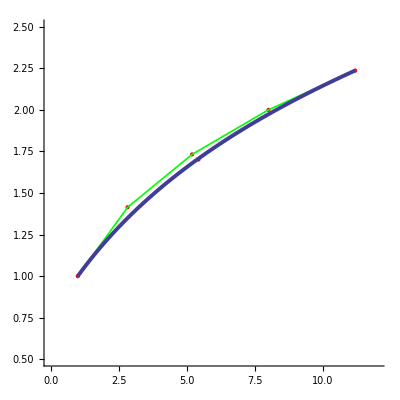

```mathematica
f=BezierFunction[bb];
gControl=Graphics[{Red,Point[bb],Thickness[0.003],Green,Line[bb]}];
gCurve=ParametricPlot[f[t],{t,0,1},PlotStyle->{Thickness[0.007]}];
gPoint=Graphics[{PointSize[Large],Red,Point[f[0.5]]}];
Show[{gControl,gPoint,gCurve},AspectRatio->1/1, Axes->True, PlotRange->{{0,12},{0.5,2.5}}]
```

## Problem 2 & 4

```mathematica
first[f_,t_]:={
Graphics[{Red,Arrow[{f[t],f[t]+Normalize[f'[t]]}]}]
};
second[f_,t_]:={
Graphics[{Black,Arrow[{f[t],f[t]+Normalize[f''[t]]}]}]
};
Manipulate[Show[{gControl,gPoint,gCurve,first[f,t],second[f,t]},AspectRatio->1/1, Axes->True, PlotRange->{{0,12},{0.5,2.5}}],{t,0,1}]
```

## Problem3

```mathematica
DegreeElevaion[pts_]:=
(
n=Length[pts]-1;
newPts=Join[{pts[[1]]},Table[i/(n+1)*pts[[i]]+(1-i/(n+1))*pts[[i+1]],{i,1,n}],{pts[[Length[pts]]]}];
Print["New control points are: ",newPts];
Return[newPts];
);

Print["Original control points are: ",cc];
cc1=DegreeElevaion[cc];
cc2=DegreeElevaion[cc1];

gcc=Graphics3D[{Thick,Red,BezierCurve[cc,SplineDegree->3],Black,Thick,Line[cc],Black,PointSize[Large],Point[cc]},Axes->True];
gcc1=Graphics3D[{Thick,Red,BezierCurve[cc1,SplineDegree->4],Green,Thick,Line[cc1],Blue,PointSize[Large],Point[cc1]},Axes->True];
gcc2=Graphics3D[{Thick,Green,BezierCurve[cc2,SplineDegree->5],Blue,Thick,Line[cc2],Red,PointSize[Large],Point[cc2]},Axes->True];
Show[{gcc,gcc1,gcc2}]
```

Original control points are: {{0,0,0},{1,3,0},{3,3,0},{4,0,3}}

New control points are: {{0,0,0},{3/4,9/4,0},{2,3,0},{13/4,9/4,3/4},{4,0,3}}

New control points are: {{0,0,0},{3/5,9/5,0},{3/2,27/10,0},{5/2,27/10,3/10},{17/5,9/5,6/5},{4,0,3}}

-Graphics3D-